```mathematica
l=0; (*0,1,2 *) 
n= 1  (*1,2,3 *) 
m = 0 (* -1,0,1 *) 

(* This animation shows the spatial probability density of finding an electron in a hydrogen atom.The Hydrogen wavefunctions transitioning between states with different quantum numbers 𝒏,𝒍,𝒎.The quantum numbers 𝒏,𝒍,𝒎 are the parameters which specify the state of the hydrogen atom:• 𝒏:total energy
• 𝒍:total angular momentum
• 𝒎:z-component of angular momentum*) 



p=Function[{x,y,z}, Abs[Re[ P[√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]]]]];

ψ2[r_, θ_, ϕ_]:= Exp[-(2 r)/n] ((2 r)/n)^(2 l) (LaguerreL[n-l-1,2 l+1, (2 r)/n] LegendreP[l,Abs[m], Cos[θ]] Cos[m ϕ])^2;

Ao=1/NIntegrate[r^2 Sin[θ]  ψ2[r, θ, ϕ], {r, 0, ∞}, {θ, 0,π}, {ϕ, 0, 2 π}];

P[r_, θ_, ϕ_]:=Ao ψ2[r, θ, ϕ];
```

1

0

```mathematica
{{1,2,3,4}}
```

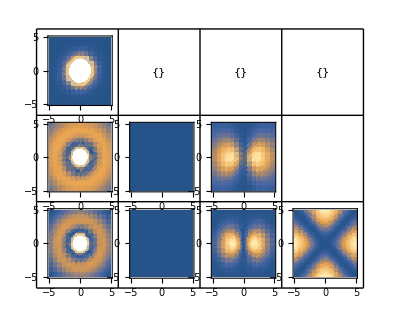

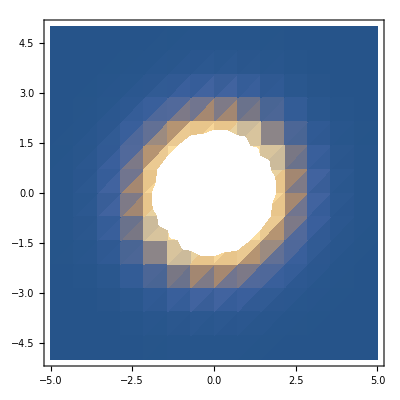

```mathematica
plot[ninput_,linput_,minput_]:= Module[{}, 
n=ninput;l=linput;m=minput;
If[ninput≤linput, l=0];
 If[linput<Abs[minput], m=0];
 Return[ DensityPlot[p[x,y,0],{x,-5,5},{y,-5,5}]]];

GraphicsGrid[{{plot[1,0,0],{}  ,{} ,{}}, 
 {plot[2,0,0],plot[2,1,0],plot[2,1,1]},{plot[3,0,0],plot[3,1,0],plot[3,1,1],plot[3,2,2]}},Frame->All]
```

```mathematica
ResourceFunction["MaTeXInstall"]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
[]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

```mathematica
Text[MaTeX["\\color{black} l"]]
```

-Graphics-

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];
```

```mathematica
SetDirectory[NotebookDirectory[]]

Clear[drawLadder];
drawLadder[n_,l_,m_,imsize_:500]:=Module[{maxrungs=5,mag=4},Graphics[{White,Opacity[1],Thickness[.02],Dashing[None],Table[Line[{{0,k},{1,k}}],{k,maxrungs}],(*draw n lines*)Gray,Dashed,Thickness[.005],Line[{{0,0},{1,0}}],ResourceFunction["HexToColor"]["#1E4886"],Opacity[.75],Disk[{0.5,n},.3],White,Opacity[1],Thickness[.02],Dashing[None],Table[Line[{{2,k},{3,k}}],{k,0,Floor[n+0.01]-1}],(*draw l lines*)Gray,Dashed,Thickness[.005],Table[Line[{{2,k},{3,k}}],{k,Floor[n+0.01],maxrungs}],ResourceFunction["HexToColor"]["#1E4886"],Opacity[.75],Disk[{2.5,l},.3],White,Opacity[1],Thickness[.02],Dashing[None],Table[Line[{{4,k},{5,k}}],{k,0,Ceiling[l-0.01]}],(*draw m lines*)Gray,Dashed,Thickness[.005],Table[Line[{{4,k},{5,k}}],{k,Ceiling[l-0.01]+1,maxrungs}],ResourceFunction["HexToColor"]["#1E4886"],Opacity[.75],Disk[{4.5,m},.3],White,Opacity[1],Thick,Dashing[None],Text[MaTeX["\\color{black} n",Magnification->mag],{.5,maxrungs+1}],Text[MaTeX["\\color{black} l",Magnification->mag],{2.5,maxrungs+1}],Text[MaTeX["\\color{black} m",Magnification->mag],{4.5,maxrungs+1}],Table[Text[MaTeX["\\color{black} "<>ToString[k],Magnification->.5*mag],{5.8,k}],{k,0,maxrungs}]},(*Background->Black,*)Background->Transparent,ImageSize->imsize]];
(*drawLadder[3,2,0]*)
Clear[drawFrame];
drawFrame[{n1_,l1_,m1_},{n2_,l2_,m2_},c1_,c2_]:=Module[{c1norm,c2norm},c1norm=c1/√(Abs[c1]^2+Abs[c2]^2);
c2norm=c2/√(Abs[c1]^2+Abs[c2]^2);
ListDensityPlot[Table[Module[{r=Norm[{x,0,z}],eq1,eq2},eq1=√(4 π) r (Exp[-r/n1] r^l1 LaguerreL[n1-1-l1,2 l1+1,(2 r)/n1]) SphericalHarmonicY[l1,m1,ArcCos[z/r],ArcTan[x,0]];
eq2=√(4 π) r (Exp[-r/n2] r^l2 LaguerreL[n2-1-l2,2 l2+1,(2 r)/n2]) SphericalHarmonicY[l2,m2,ArcCos[z/r],ArcTan[x,0]];
Abs[c1norm*eq1+c2norm*eq2]^2],{z,-40.1,40,.5},{x,-40.1,80,.5}],DataRange->{{-40,40},{-40,80}},AspectRatio->.8/1.2,ImageSize->1000*{1.2,.8},Mesh->False,Frame->False,ColorFunctionScaling->True,ColorFunction->rainbow,Epilog->Inset[drawLadder[n1*c1norm^2+n2*c2norm^2,l1*c1norm^2+l2*c2norm^2,m1*c1norm^2+m2*c2norm^2,250],{29,20}]]]
```

/Users/tomikbaikie/Cambridge University Dropbox/Tomi Baikie/website/animation

```mathematica
drawFramedata[{n1_,l1_,m1_},{n2_,l2_,m2_},c1_,c2_]:=Module[{c1norm,c2norm},c1norm=c1/√(Abs[c1]^2+Abs[c2]^2);
c2norm=c2/√(Abs[c1]^2+Abs[c2]^2);
Table[Module[{r=Norm[{x,0,z}],eq1,eq2},eq1=√(4 π) r (Exp[-r/n1] r^l1 LaguerreL[n1-1-l1,2 l1+1,(2 r)/n1]) SphericalHarmonicY[l1,m1,ArcCos[z/r],ArcTan[x,0]];
eq2=√(4 π) r (Exp[-r/n2] r^l2 LaguerreL[n2-1-l2,2 l2+1,(2 r)/n2]) SphericalHarmonicY[l2,m2,ArcCos[z/r],ArcTan[x,0]];
Abs[c1norm*eq1+c2norm*eq2]^2],{z,-40.1,40,.5},{x,-40.1,80,.5}]]
```

```mathematica
ResourceFunction["HexToColor"][#]&/@{"#3E9398","#B74344","#CE6A69","#DFA3A6","#F1D1CC"}
```

{#3E9398,#B74344,#CE6A69,#DFA3A6,#F1D1CC}

```mathematica
colz= ResourceFunction["HexToColor"][#]&/@Reverse[{"#CDE4F7","#A5C9E8","#6294CA","#306EAB","#1E4886","#3E9398"}]

rainbow[z_]:=Blend[colz,z]
(*rainbow[_,_,z_]:=rainbow[z]*)
```

{RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.11764705882352941, 0.2823529411764706, 0.5254901960784314],RGBColor[0.18823529411764706, 0.43137254901960786, 0.6705882352941176],RGBColor[0.38431372549019605, 0.580392156862745, 0.792156862745098],RGBColor[0.6470588235294118, 0.788235294117647, 0.9098039215686274],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922]}

```mathematica
Table
```

{RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.11764705882352941, 0.2823529411764706, 0.5254901960784314],RGBColor[0.18823529411764706, 0.43137254901960786, 0.6705882352941176],RGBColor[0.38431372549019605, 0.580392156862745, 0.792156862745098],RGBColor[0.6470588235294118, 0.788235294117647, 0.9098039215686274],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922]}

```mathematica
Table[rainbow[x],{x,-10,100,1}]
```

{RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.24313725490196078, 0.5764705882352941, 0.596078431372549],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922],RGBColor[0.803921568627451, 0.8941176470588235, 0.9686274509803922]}

```mathematica
Max[drawFramedata[{1,1,1},{2,1,1},.5,.5]]
```

3.51009

```mathematica
drawFrame[{4,3,1},{1,1,1},.5,.5]
```

-Graphics-

```mathematica
Clear[renderFrame];
renderFrame[t_]:=Module[{tt=t-Floor[t],c1,c2,ttt},ttt=Piecewise[{{0,tt<.1},{(tt-.1)/(1-.1-.1),.1<=tt<.9},{1,tt>=.9}}];
c1=Cos[π/2*ttt];
c2=Sin[π/2*ttt];
Switch[Floor[t],0,drawFrame[{5,0,0},{4,0,0},c1,c2],1,drawFrame[{4,0,0},{3,0,0},c1,c2],2,drawFrame[{3,0,0},{3,1,0},c1,c2],3,drawFrame[{3,1,0},{3,1,1},c1,c2],4,drawFrame[{3,1,1},{4,0,0},c1,c2],5,drawFrame[{4,0,0},{4,1,1},c1,c2],6,drawFrame[{4,1,1},{4,2,1},c1,c2],7,drawFrame[{4,2,1},{4,3,1},c1,c2],8,drawFrame[{4,3,1},{5,0,0},c1,c2],9,drawFrame[{5,0,0},{5,1,1},c1,c2],10,drawFrame[{5,1,1},{5,2,1},c1,c2],11,drawFrame[{5,2,1},{5,3,1},c1,c2],12,drawFrame[{5,3,1},{5,4,1},c1,c2],13,drawFrame[{5,4,1},{5,3,1},c1,c2],14,drawFrame[{5,3,1},{5,2,1},c1,c2],15,drawFrame[{5,2,1},{5,1,1},c1,c2],16,drawFrame[{5,1,1},{4,1,1},c1,c2],17,drawFrame[{4,1,1},{3,1,1},c1,c2],18,drawFrame[{3,1,1},{2,1,1},c1,c2],19,drawFrame[{2,1,1},{1,0,0},c1,c2],_,drawFrame[{2,1,0},{1,0,0},0,1]]];
(*renderFrame[0.9]*)
```

```mathematica
saveframe[tt_]:=Module[{frame,title},frame=renderFrame[tt];
title=IntegerString[Floor[tt*1000],10,8]<>".png";
Export["frames/"<>title,frame];];
```

```mathematica
Monitor[Table[saveframe[t],{t,0,20,1/120}],ProgressIndicator[t,{0,20}]];
```